```mathematica
(* Simulation to check single traveling wave solution behavior *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=1000; 
maxtime=20000;
verbose=False;
veryverbose=False;
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Testing two trait evolution *)
r=0.5;
genotypes={{1,1},{2,1},{3,1},{4,1},{5,1},{6,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulations to compare *)
SeedRandom[100];
fulldata=0;
results0=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
SeedRandom[100];
fulldata=1;
results1=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
```

```mathematica
(* Compare Data Collected *)
comparedata0=results0[[;;,1;;10]];
comparedata1 = getSummarizedResults[results1,Δc1,Δc2,popsize];
Total[comparedata0-comparedata1]
```

{0.,0.,0.,0.,-3.16026×10^-18,3.47982×10^-18,-2.29364×10^-17,0.,-6.43929×10^-15,0.}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Linear combination experiment w/ evolution in 2 dimensions *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.02,0.02,2 10^-4,2 10^-4,10^7};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactflag}={0,False,False,False};
```

```mathematica
(* Run simulation *)
SeedRandom[7];
simdata=ParallelTable[
(* Set initial genotypes and their abundances *)
Print["Trial ",i];
λ1=(Mod[i,21,1]-1)/20;
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2];
results=RunSimulationCheckEachMutation2[popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/v2dtest/v2dtest_N-10p7_c-0d02_U-2x10pn4_exp"<>ToString[i]<>".m",{results,popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2}];
{Mean[results[[;;,9]]],popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2}
,{i,1,210}];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store only summary data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^10};
{starttime,timestep,maxtime}={0,1000,30000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 8. in Concurrent Mutations Regime with expected time scale 65.7881 and rate of adaptation 0.000152003

Trait 2 q = 8. in Concurrent Mutations Regime with expected time scale 65.7881 and rate of adaptation 0.000152003

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.m",results];
```

mean substitution load = 0.077788

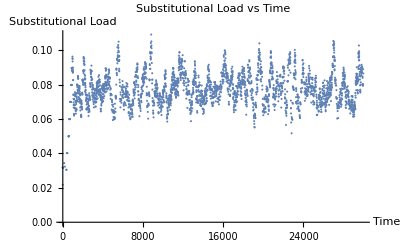

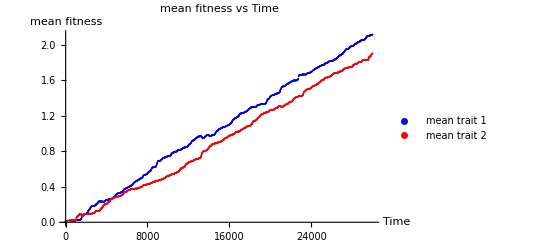

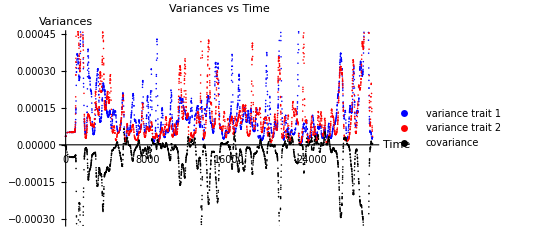

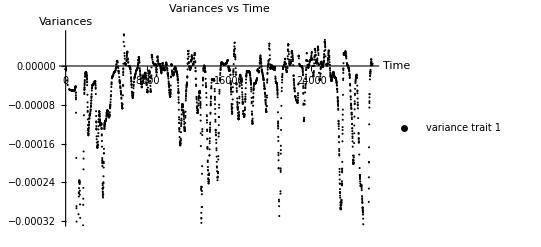

mean covariance -0.0000756336

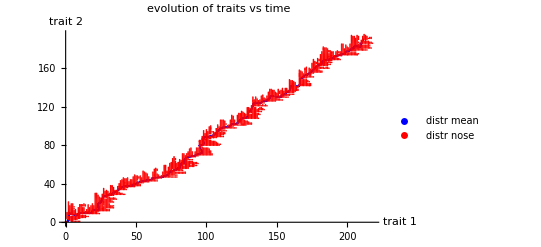

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.m"];
meansubload=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
timesAndMean1=Table[{results[[i]][[1]],results[[i]][[2]]},{i,1,Length[results]}];
timesAndMean2=Table[{results[[i]][[1]],results[[i]][[3]]},{i,1,Length[results]}];
timesAndVar1=Table[{results[[i]][[1]],results[[i]][[6]]},{i,1,Length[results]}];
timesAndVar2=Table[{results[[i]][[1]],results[[i]][[7]]},{i,1,Length[results]}];
timesAndCov=Table[{results[[i]][[1]],results[[i]][[5]]},{i,1,Length[results]}];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
Print["mean substitution load = ",meansubload];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
ListPlot[{timesAndMean1,timesAndMean2},PlotStyle->{Blue,Red},PlotLegends->{"mean trait 1","mean trait 2"},AxesLabel->{"Time","mean fitness"},PlotLabel->"mean fitness vs Time"]
ListPlot[{timesAndVar1,timesAndVar2,timesAndCov},PlotStyle->{Blue,Red,Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
ListPlot[{timesAndCov},PlotStyle->{Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
Print["mean covariance ",Mean[timesAndCov[[;;,2]]]];
ListPlot[{mean2mean,noseTravel},PlotStyle->{Blue,Red},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"evolution of traits vs time"]
```

```mathematica
check=Table[If[results[[i]][[-1]]=={0,0},{results[[i]][[1]],results[[i]][[5]],0},{results[[i]][[1]],results[[i]][[5]],1}],{i,1,Length[results]}];
```

{{1000.,-0.0000602821,0},{1002.82,-0.0000649679,1},{1002.9,-0.0000651173,1},{1004.75,-0.0000686083,1},{1015.59,-0.0000964096,1},{1037.65,-0.000189531,1},{1058.19,-0.000289069,1},{1059.14,-0.000293177,1},{1066.05,-0.000320842,1},{1073.7,-0.000346553,1},{1080.25,-0.000364322,1},{1087.62,-0.000379925,1},{1115.5,-0.000407002,1},{1117.25,-0.000407485,1},{1125.14,-0.000408461,1},{1129.75,-0.000408241,1},{1133.2,-0.000407752,1},{1172.97,-0.000388938,1},{1175.56,-0.000387129,1},{1178.77,-0.000384809,1},{1181.48,-0.000382789,1},{1202.43,-0.000365355,1},{1202.96,-0.000364873,1},{1210.94,-0.000357379,1},{1222.22,-0.00034602,1},{1228.43,-0.000339399,1},{1231.63,-0.000335888,1},{1234.75,-0.000332398,1},{1257.32,-0.000305671,1},{1287.83,-0.000269069,1},{1294.11,-0.000262292,1},{1296.,-0.000260355,1},{1305.07,-0.000251786,1},{1321.52,-0.000240189,1},{1326.56,-0.000237844,1},{1327.24,-0.000237576,1},{1334.38,-0.000235453,1},{1354.36,-0.000236631,1},{1360.73,-0.000239256,1},{1361.73,-0.000239765,1},{1363.27,-0.000240607,1},{1367.45,-0.0002432,1},{1383.26,-0.000257154,1},{1390.22,-0.000265344,1},{1404.11,-0.00028534,1},{1419.46,-0.00031313,1},{1429.27,-0.000334079,1},{1432.32,-0.000341099,1},{1432.41,-0.000341311,1},{1436.92,-0.000352158,1},{1441.22,-0.000363024,1},{1446.68,-0.000377574,1},{1464.29,-0.000430134,1},{1489.73,-0.000521223,1},{1492.26,-0.000531178,1},{1505.12,-0.00058353,1},{1515.95,-0.000628921,1},{1516.1,-0.000629587,1},{1517.98,-0.000637439,1},{1519.95,-0.000645677,1},{1521.3,-0.000651315,1},{1523.95,-0.000662268,1},{1529.35,-0.000684166,1},{1532.65,-0.000697122,1},{1562.28,-0.000784795,1},{1569.23,-0.000793556,1},{1587.98,-0.000786358,1},{1598.94,-0.000760872,1},{1605.15,-0.000740292,1},{1612.53,-0.000711042,1},{1618.22,-0.00068581,1},{1622.31,-0.000666547,1},{1623.38,-0.000661384,1},{1629.87,-0.000629455,1},{1630.26,-0.000627479,1},{1655.1,-0.000506039,1},{1665.85,-0.000458878,1},{1672.6,-0.000431533,1},{1675.99,-0.000418453,1},{1682.17,-0.000395634,1},{1692.45,-0.000360259,1},{1697.89,-0.000342592,1},{1699.42,-0.000337726,1},{1702.35,-0.000328551,1},{1716.35,-0.000286314,1},{1720.69,-0.000273635,1},{1728.48,-0.000251296,1},{1742.27,-0.000213024,1},{1750.58,-0.000190937,1},{1756.34,-0.000176241,1},{1791.53,-0.000101488,1},{1825.24,-0.0000578032,1},{1828.43,-0.0000548901,1},{1835.05,-0.0000493684,1},{1836.61,-0.0000481702,1},{1837.24,-0.0000476926,1},{1841.18,-0.000044853,1},{1842.81,-0.0000437396,1},{1850.07,-0.0000391822,1},{1854.13,-0.0000368989,1},{1857.98,-0.0000348944,1},{1866.21,-0.0000310737,1},{1871.09,-0.0000290797,1},{1893.11,-0.0000220664,1},{1896.04,-0.0000213347,1},{1910.22,-0.0000183385,1},{1925.81,-0.000015905,1},{1930.66,-0.0000153039,1},{1936.64,-0.0000146521,1},{1950.7,-0.0000134787,1},{1953.05,-0.0000133286,1},{1980.01,-0.0000124523,1},{1982.67,-0.0000124472,1},{1985.09,-0.0000124551,1},{1985.3,-0.0000124564,1},{1987.82,-0.0000124783,1},{1988.9,-0.0000124917,1},{1989.3,-0.0000124973,1},{2000.,-0.0000127709,0}}

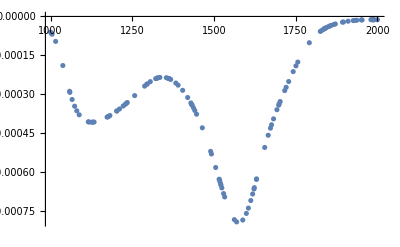

```mathematica
check[[56;;174]]
ListPlot[check[[56;;174,1;;2]]]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^10};
{starttime,timestep,maxtime}={0,1000,30000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 8. in Concurrent Mutations Regime with expected time scale 65.7881 and rate of adaptation 0.000152003

Trait 2 q = 8. in Concurrent Mutations Regime with expected time scale 65.7881 and rate of adaptation 0.000152003

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m",results];
```